```mathematica
(* Dimension de Hausdorff par box-counting direct *) 
(* Méthode boîte par boîte (brutal) *)
(* la liste doit être un sous-intervalle ordonné de [0,1] *)
Clear[brut];
brut[list_,n_]:=Block[{templ=list,pt,b,δ=8,weight,weights={}},
b=δ^-n;
pt=templ[[1]];
While[b≤1,
weight=0;
While[pt≤b,
weight++;
If[Length[templ]>1,templ=Rest[templ],Break[]];
pt=templ[[1]];];
If[weight>0,AppendTo[weights,weight]];
b+=δ^-n;];
Print[Log[Length[weights]]/(n Log[δ])//N];]
```

```mathematica
(* Méthode point par point (moins brutal ?) *)
(* la liste doit être un sous-intervalle ordonné de [0,1] *)
Clear[haus];
haus[list_,n_]:=Block[{templ=list,curpt,refpt,refval,b,δ=8,nboxes=0,len=Length[list]},
b=δ^-n;
refpt=1;refval=list[[1]];curpt=2;
While[curpt≤len,
While[(list[[curpt]]-refval≤b)&&curpt<len,curpt++;];
refval=list[[curpt]];
curpt+=1;nboxes++;
];
Print[Log[nboxes]/(n Log[δ])//N];]
```

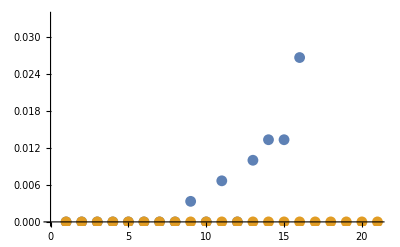

```mathematica
l={0,0.2,0.4,1};
listn=Table[it,{it,1,5,.2}];
timebrut=ParallelMap[Timing[brut[l,#]][[1]]&,listn];
timehaus=ParallelMap[Timing[haus[l,#]][[1]]&,listn];
ListPlot[{timebrut,timehaus}]
```

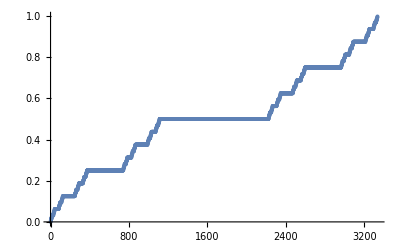

```mathematica
ClearAll[cSet,int];
int=Table[it,{it,0,1,0.0003}];
cSet=ParallelMap[CantorStaircase,int];
ListPlot[cSet]
```

```mathematica
(* système de test *)
(*amplitude de saut entre les sites atomiques i et i+1*)
Clear[t];
t[i_]:=Block[{k,tt},k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]

(*hamiltonien avec conditions aux bords libres*)
Clear[h];
h[n_]:=Block[{tbl,ar},tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]]

(* spectre *)
spect[n_,rr_?NumberQ,vv_?NumberQ]:=Block[{spec,r=rr,v=vv},
spec=Sort[Eigenvalues[h[n]]];
spec=(spec-spec[[1]])/(spec[[-1]]-spec[[1]]);
Return[spec];]
```

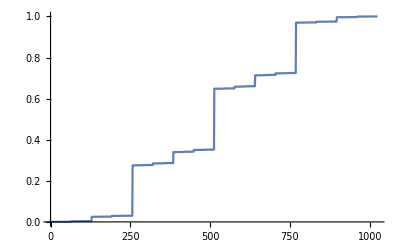

```mathematica
ListPlot[spect[10,.3,1.],Joined->True]
```

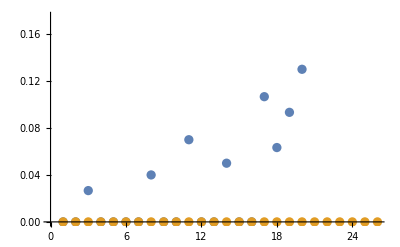

```mathematica
l=spect[10,.3,1.];
listn=Table[it,{it,1,6,.2}];
timebrut=ParallelMap[Timing[brut[l,#]][[1]]&,listn];
timehaus=ParallelMap[Timing[haus[l,#]][[1]]&,listn];
ListPlot[{timebrut,timehaus}]
```

```mathematica
(* Méthode point par point (moins brutal) *)
(* la liste doit être un sous-intervalle ordonné de [0,1] *)
Clear[haus];
haus[list_,n_,δ_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,nboxes=0,len=Length[list],loop},
(* Δ: distance btw the left side of the current box and the current pt *)
Δ=list[[curLbl]]-curBS;
While[curLbl≤len,
loop=False;
(* while the current pt is in the current box, pass to the pt on its right *)
While[Δ≤b&&curLbl<len,curLbl++;Δ=list[[curLbl]]-curBS;loop=True;];
(* after the loop the current box has jumped of Floor[Δ/b] units, and one more box has points in it *)
If[loop,
curBS+=b Floor[Δ/b];nboxes++;Δ=list[[curLbl]]-curBS;,
curLbl++;];
];
Return[nboxes];]
```

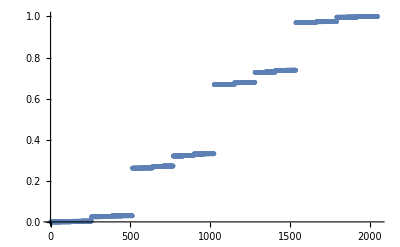

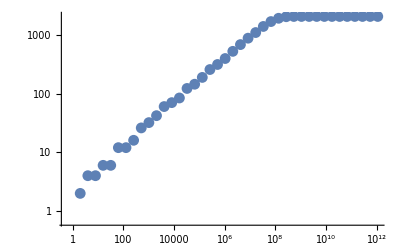

```mathematica
sp=spect[11,.3,.9];
ListPlot[sp]
r=Range[1,40,1];
delta=2;
nb=ParallelMap[haus[sp,#,delta]&,r];
(* number of filled boxes as a function of their length *)
dat=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
ListLogLogPlot[dat]
```

```mathematica
fit=LinearModelFit[Log10@dat[[16;;16+8]],logl,logl];
Plot[Normal@fit,{logl,0,12},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat}]
```

-Graphics-

```mathematica
fit
```

FittedModel[0.409824+0.364879 logl]

```mathematica
1/Log2[(.3)/2]
```

-0.365368